```mathematica
S[k_] := (Sin[k aa] + (k / uu) Exp[I k aa]) / (Sin[k aa] + (k / uu) Exp[-I k aa])
```

```mathematica
aa := 2
```

```mathematica
uu := 1
```

```mathematica
U[k_] := Arg[S[k]]
```

```mathematica
S[k]
```

(-1/10 ⅇ^(ⅈ k) k+Sin[k])/(-1/10 ⅇ^(-ⅈ k) k+Sin[k])

```mathematica
S[Pi]
```

1

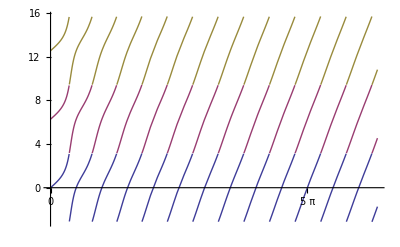

```mathematica
Plot[{U[k], U[k] + 2 * Pi, U[k] + 4 * Pi}, {k, 0.0, 20.0}, Ticks->{Range[0, 20 * Pi, Pi], Automatic}]
```